```mathematica
A=Import["/Users/alex/Desktop/Book1.csv"]
```

```mathematica
A={{"Цвет","Градус","","Длина волны"},{"Фиолетовый","174°58’51’’","",404.66},{"Фиолетовый","174°3’37’’","",435.83},{"Синий","172°23’44’’","",491.6},{"Синий","172°15’40’’","",""},{"Синий","172°3’37’’","",""},{"Голубой","172°0’28’’","",""},{"Голубой","171°45’44’’","",""},{"Голубой","171°4’21’’","",""},{"Зеленый","170°44’52’’","",546.07},{"Желтый","169°48’35’’","",576.96},{"Желтый","169°54’50’’","",579.07},{"Красный","168°23’24’’","",623.4},{"Фиолетовый","160°21’50’’","",""},{"Фиолетовый","156°36’27’’","",""},{"Зеленый","152°45’54’’","",""},{"Желтый","150°28’38’’","",""},{"Желтый","150°19’33’’","",""},{"Фиолетовый","144°26’50’’","",""}};
```

```mathematica
Angle0 = FromDMS[{186,44,36}]Degree
```

(56023 °)/300

```mathematica
A[[1,3]]="sin Δϕ";
A[[1,4]]="λ, нм";
```

```mathematica
For[i = 2, i<20, i++,
A[[i,3]]=N[Sin[Angle0-FromDMS[A[[i,2]]]Degree]];
]
```

```mathematica
Grid[A, Frame->All]
```

Цвет | Градус | sin Δϕ | λ, нм
Фиолетовый | 174°58’51’’ | 0.204097 | 404.66
Фиолетовый | 174°3’37’’ | 0.219733 | 435.83
Синий | 172°23’44’’ | 0.248014 | 491.6
Синий | 172°15’40’’ | 0.250267 | 
Синий | 172°3’37’’ | 0.253645 | 
Голубой | 172°0’28’’ | 0.254489 | 
Голубой | 171°45’44’’ | 0.258707 | 
Голубой | 171°4’21’’ | 0.270208 | 
Зеленый | 170°44’52’’ | 0.275805 | 546.07
Желтый | 169°48’35’’ | 0.291426 | 576.96
Желтый | 169°54’50’’ | 0.289756 | 579.07
Красный | 168°23’24’’ | 0.314987 | 623.4
Фиолетовый | 160°21’50’’ | 0.444531 | 
Фиолетовый | 156°36’27’’ | 0.502165 | 
Зеленый | 152°45’54’’ | 0.559096 | 
Желтый | 150°28’38’’ | 0.591685 | 
Желтый | 150°19’33’’ | 0.593793 | 
Фиолетовый | 144°26’50’’ | 0.673142 |

```mathematica
Export["Table.pdf",Grid[A, Frame->All]]
```

Table.pdf

```mathematica
B=ArrayFlatten[{{A[[1;;4,1;;4]]},{A[[10;;13,1;;4]]}}];
Grid[B,Frame->All]
```

Цвет | Градус | sin Δϕ | λ, нм
Фиолетовый | 174°58’51’’ | 0.204097 | 404.66
Фиолетовый | 174°3’37’’ | 0.219733 | 435.83
Синий | 172°23’44’’ | 0.248014 | 491.6
Зеленый | 170°44’52’’ | 0.275805 | 546.07
Желтый | 169°48’35’’ | 0.291426 | 576.96
Желтый | 169°54’50’’ | 0.289756 | 579.07
Красный | 168°23’24’’ | 0.314987 | 623.4

{Cos[(3533 °)/300]/(360 √2),Cos[(952 °)/75]/(360 √2),Cos[(359 °)/25]/(360 √2),Cos[(1601 °)/100]/(360 √2),Cos[(5083 °)/300]/(360 √2),Cos[(5053 °)/300]/(360 √2),Cos[(459 °)/25]/(360 √2)}

{ErrorBar[0,Cos[(3533 °)/300]/(360 √2)],ErrorBar[0,Cos[(952 °)/75]/(360 √2)],ErrorBar[0,Cos[(359 °)/25]/(360 √2)],ErrorBar[0,Cos[(1601 °)/100]/(360 √2)],ErrorBar[0,Cos[(5083 °)/300]/(360 √2)],ErrorBar[0,Cos[(5053 °)/300]/(360 √2)],ErrorBar[0,Cos[(459 °)/25]/(360 √2)]}

404.66 | 0.204097
435.83 | 0.219733
491.6 | 0.248014
546.07 | 0.275805
576.96 | 0.291426
579.07 | 0.289756
623.4 | 0.314987

0.000343567+0.00050345 x

{{{404.66,0.204097},ErrorBar[0,Cos[(3533 °)/300]/(360 √2)]},{{435.83,0.219733},ErrorBar[0,Cos[(952 °)/75]/(360 √2)]},{{491.6,0.248014},ErrorBar[0,Cos[(359 °)/25]/(360 √2)]},{{546.07,0.275805},ErrorBar[0,Cos[(1601 °)/100]/(360 √2)]},{{576.96,0.291426},ErrorBar[0,Cos[(5083 °)/300]/(360 √2)]},{{579.07,0.289756},ErrorBar[0,Cos[(5053 °)/300]/(360 √2)]},{{623.4,0.314987},ErrorBar[0,Cos[(459 °)/25]/(360 √2)]}}

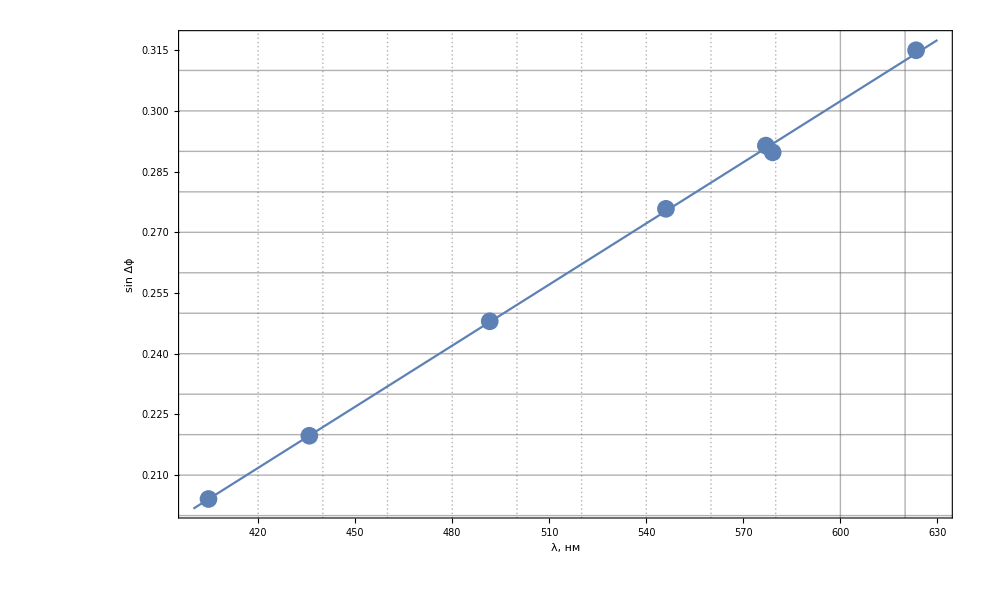

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000343567 | 0.00287562 | 0.119476 | 0.90955
x | 0.00050345 | 5.44778×10^-6 | 92.4137 | 2.8124×10^-9

1986.3

```mathematica
Needs["ErrorBarPlots`"];
graphErrorTableY = Table[0,7];
grpahErrorTableX = Table[0,7];
errorValues = Table[0,7];
For[i=2,i<9,i++,
graphErrorTableY[[i-1]]=Sqrt[Cos[Angle0-FromDMS[B[[i,2]]] Degree]^2*(FromDMS[{0,0,5}])^2+(-Cos[Angle0-FromDMS[B[[i,2]]] Degree])^2*(FromDMS[{0,0,5}])^2];
grpahErrorTableX[[i-1]]=0;
errorValues[[i-1]]=ErrorBar[grpahErrorTableX[[i-1]],graphErrorTableY[[i-1]]];
]
graphErrorTableY
errorValues
PlotPart = B[[2;;8,3;;4]];
PlotPart=PlotPart.({{0, 1}, {1, 0}});
Grid[PlotPart, Frame->All]
ApproximationLine = LinearModelFit[PlotPart,x,x];
Normal[ApproximationLine]
PlotPart=Partition[Riffle[PlotPart, errorValues],2]
Show[ErrorListPlot[PlotPart,PlotRange->Automatic, PlotTheme->"Detailed",Joined->False, GridLines->All],Plot[ApproximationLine[x],{x,400,630}], PlotRange->Automatic,FrameLabel->{{HoldForm[sin Δϕ],None},{RawBoxes[RowBox[{"λ",","," ","нм"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
ApproximationLine["ParameterTable"]
1/ApproximationLine["BestFitParameters"][[2]]
```

```mathematica
Needs["ErrorBarPlots`"];
graphErrorTableY = Table[0,7];
grpahErrorTableX = Table[0,7];
errorValues = Table[0,7];
For[i=2,i<9,i++,
graphErrorTableY[[i-1]]=Sqrt[Cos[Angle0-FromDMS[B[[i,2]]] Degree]^2*(FromDMS[{0,0,5}])^2+(-Cos[Angle0-FromDMS[B[[i,2]]] Degree])^2*(FromDMS[{0,0,5}])^2];
grpahErrorTableX[[i-1]]=0;
errorValues[[i-1]]=ErrorBar[graphErrorTableY[[i-1]], grpahErrorTableX[[i-1]]];
]
PlotPart = B[[2;;8,3;;4]];
ApproximationLine = LinearModelFit[PlotPart,x,x];
ApproximationLine["ParameterTable"]
1/ApproximationLine["BestFitParameters"][[2]]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.376295 | 5.71583 | -0.0658338 | 0.950061
x | 1985.13 | 21.4809 | 92.4137 | 2.8124×10^-9

0.000503744

```mathematica
Export["/Users/alex/Desktop/data.pdf", ApproximationLine["ParameterTable"]]
```

/Users/alex/Desktop/data.pdf

```mathematica
Export["Table2.pdf", Grid[B,Frame->All]]
```

Table2.pdf

Порядок дифракции | Угол первой линии | Угол второй линии | ∆φ | D экспериментальня | D теоретическая
1 | 169°48'35'' | 169°54'50'' | 375 | 10.6018 | 10.4458
2 | 150°28'38'' | 150°19'33'' | 545 | 24.5548 | 24.509
-1 | 203°23'37'' | 203°27'15'' | 218 | 10.9867 | 10.4458
-2 | 221°19'33'' | 221°28'2'' | 509 | 26.2245 | 24.509

Table2.pdf

{{1,0},{2,0},{-1,0},{-2,0}}

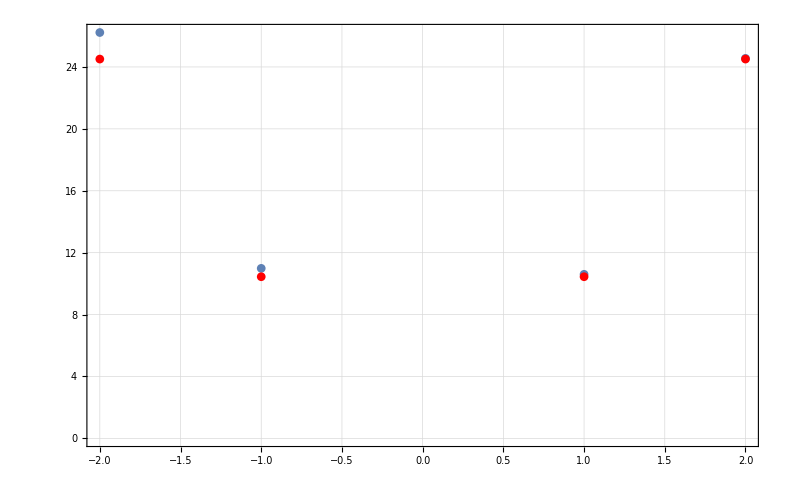

```mathematica
Table2={{"Порядок дифракции","Угол первой линии","Угол второй линии","∆φ","D экспериментальня","D теоретическая"},{1,"169°48'35''","169°54'50''","","",""},{2,"150°28'38''","150°19'33''","","",""},{-1,"203°23'37''","203°27'15''","","",""},{-2,"221°19'33''","221°28'2''","","",""}};
length[x_,y_]:=N[(Sin[Abs[FromDMS[x]-Angle0]Degree]*2000)/y];
Dispersion[m_,d_,l_]:=(m*20000)/(√(d^2-m^2 l^2));
For[i=2,i<6,i++,
Table2[[i,4]]=Abs[FromDMS[Table2[[i,2]]]-FromDMS[Table2[[i,3]]]]*3600;
Table2[[i,5]]=Abs[N[Table2[[i,4]]/((length[Table2[[i,2]],Table2[[i,1]]]-length[Table2[[i,3]],Table2[[i,1]]])*10)]];
Table2[[i,6]]=Abs[Dispersion[Table2[[i,1]],2000, (B[[7,4]]+B[[6,4]])/2]];

]
Grid[Table2,Frame->All,ItemSize->Full]
Export["Table2.pdf",Grid[Table2,Frame->All], ItemSize->All]
Experiment = PadRight[Table2[[2;;5,1;;1]],{4,2}];
Theory = Experiment
For[i=2,i<6,i++,
Experiment[[i-1,2]]=Table2[[i,5]];
Theory[[i-1,2]]=Table2[[i,6]];
]
Show[ListPlot[Experiment,PlotTheme->"Detailed",PlotMarkers->Automatic], ListPlot[Theory, PlotStyle->Red,PlotMarkers->Automatic]]
```

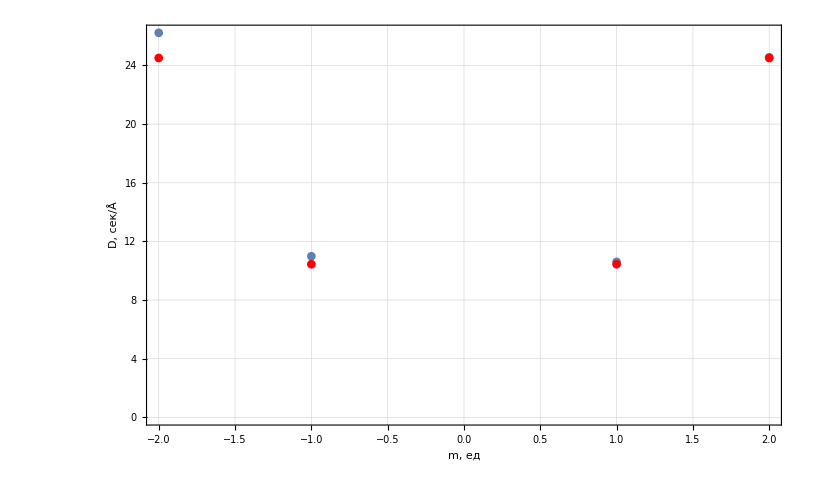

```mathematica
Show[%1792,FrameLabel->{{RawBoxes[RowBox[{"D",","," ",RowBox[{"сек","/","Å"}]}]],None},{RawBoxes[RowBox[{"m",","," ","ед"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Dispersion[2,2000,579.07]
```

24.5315

```mathematica
32/10.6018
```

3.01836